# Report Project 2

Course code: IX1501
Date: 2019-09-08

Viktor Jäger, vjager@kth.se
Sam Florin, sflorin@kth.se

Task: Winning a Teddy

## Summery

### Task

Which distribution?
In this task, randomNumber[i, n] can be used to generate data for the distributions i=1,2,…,6. They are all distributions that are mentioned in the course literature (Blom Sec. 3.4 and Sec. 3.6). Do the following assignments for each of six distributions, i.e. i∈{1,2,…,6}. 

	* Use the straight line approach to determine a distribution model.
	* Determine point estimates of the parameters.
	* Compute 95% confidence intervals for the parameters. The interval should not be longer than 10% of its mean, 		   e.g. μ (1±0.05).

### Result

## Method

### Probability function of the sum

Variables p_Xd4 - p_Xd20 are the probability functions of each individual dice. The five dices makes up the probability space: Ω={5≤x≤50}. This space has a finite set, function is discrete.

### Probability of winning the Teddy

The probability of winning a Teddy can be derived from the probability function. P(X=x), where 5≤x≤10 ∧ 45≤x≤50 gives the probability of winning.

### Expected Investment

Expected win, we use the distribution function ‘för-första-gången-fördelning’ which tries until the first time result. 
Definition: p_X(k)=(1-p)^(k-1)p, k=1,2,..., where 0<p is said to be 'för-första-gången-fördelad'

### Probability of winning with 20 attempts

Probability of winning with 20 rolls:

## Code

Straight Line Approach

#### Setup and Graph

```mathematica
SetDirectory[NotebookDirectory[]];
Once[Get["Project2.m","IX1501"]];
```

```mathematica
(* declare and generate the 6 unknown distributions *)
(* sort and plot the n points of the distributions *)
n=10000;
𝕩1=randomNumber[1,n];
𝕩2=randomNumber[2,n];
𝕩3=randomNumber[3,n];
𝕩4=randomNumber[4,n];
𝕩5=randomNumber[5,n];
𝕩6=randomNumber[6,n];

𝕩1sort=Sort[𝕩1];
𝕩2sort=Sort[𝕩2];
𝕩3sort=Sort[𝕩3];
𝕩4sort=Sort[𝕩4];
𝕩5sort=Sort[𝕩5];
𝕩6sort=Sort[𝕩6];
```

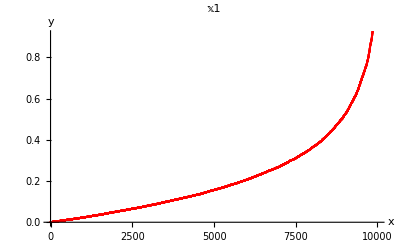

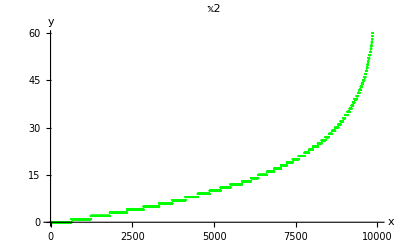

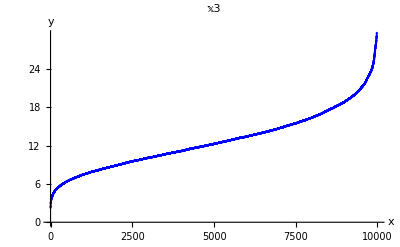

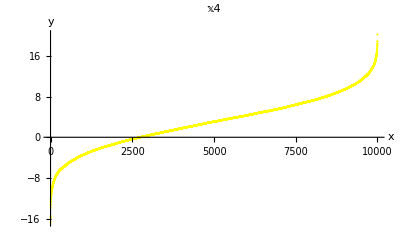

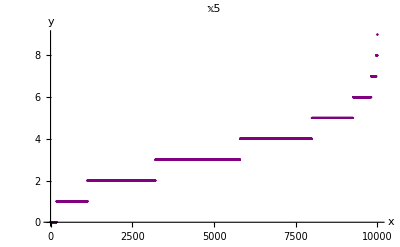

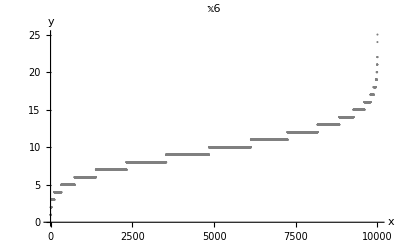

```mathematica
ListPlot[𝕩1sort,AxesLabel->{HoldForm[x],HoldForm[y]},PlotStyle->Red,PlotLabel->"𝕩1"]
ListPlot[𝕩2sort,AxesLabel->{HoldForm[x],HoldForm[y]},PlotStyle->Green,PlotLabel->"𝕩2"]
ListPlot[𝕩3sort,AxesLabel->{HoldForm[x],HoldForm[y]},PlotStyle->Blue,PlotLabel->"𝕩3"]
ListPlot[𝕩4sort,AxesLabel->{HoldForm[x],HoldForm[y]},PlotStyle->Yellow,PlotLabel->"𝕩4"]
ListPlot[𝕩5sort,AxesLabel->{HoldForm[x],HoldForm[y]},PlotStyle->Purple,PlotLabel->"𝕩5"]
ListPlot[𝕩6sort,AxesLabel->{HoldForm[x],HoldForm[y]},PlotStyle->Gray,PlotLabel->"𝕩6"]

(* Below: Plot all the unknown functions in sorted form *)
```

```mathematica
(* 
Let each value correspond to and increase of Δ=1/n probability. Also let each value correspond to the mid point in the Δinterval so the first value Subscript[x, 1] corresponds to P(X≤Subscript[x, 1])=Δ/2 and the value Subscript[x, k] to P(X≤Subscript[x, k])=Δ/2+(k-1) Δ. 
*)
```

```mathematica
Δ=1/n;
𝕡data=Δ/2+Range[0,1-Δ,Δ]//N;
```

```mathematica
(* lineplot to be used to compare the data to the model, declared "globally" here *)
lineplot=Plot[x,{x,0,1}];
```

```mathematica
𝕩1𝕡data=Transpose[{𝕩1sort,𝕡data}];
𝕩2𝕡data=Transpose[{𝕩2sort,𝕡data}];
𝕩3𝕡data=Transpose[{𝕩3sort,𝕡data}];
𝕩4𝕡data=Transpose[{𝕩4sort,𝕡data}];
𝕩5𝕡data=Transpose[{𝕩5sort,𝕡data}];
𝕩6𝕡data=Transpose[{𝕩6sort,𝕡data}];
```

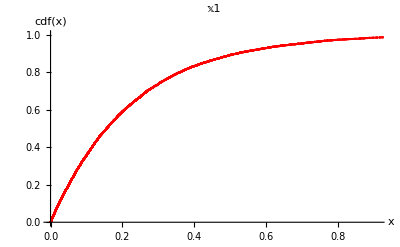

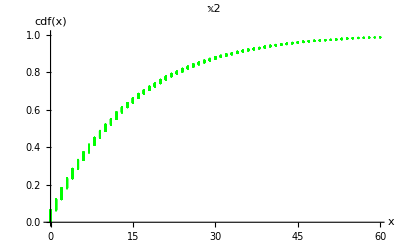

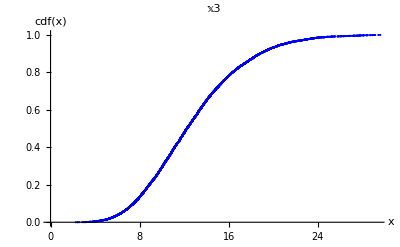

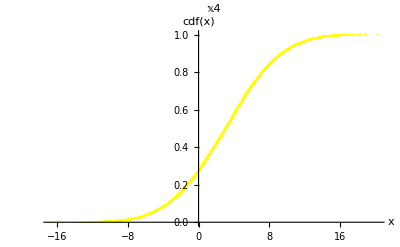

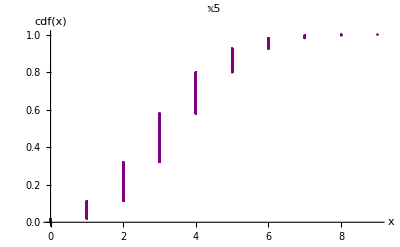

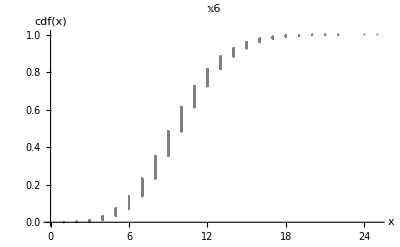

```mathematica
ListPlot[𝕩1𝕡data,AxesLabel->{HoldForm[x],HoldForm[cdf[x]]},PlotStyle->Red,PlotLabel->"𝕩1"]
ListPlot[𝕩2𝕡data,AxesLabel->{HoldForm[x],HoldForm[cdf[x]]},PlotStyle->Green,PlotLabel->"𝕩2"]
ListPlot[𝕩3𝕡data,AxesLabel->{HoldForm[x],HoldForm[cdf[x]]},PlotStyle->Blue,PlotLabel->"𝕩3"]
ListPlot[𝕩4𝕡data,AxesLabel->{HoldForm[x],HoldForm[cdf[x]]},PlotStyle->Yellow,PlotLabel->"𝕩4"]
ListPlot[𝕩5𝕡data,AxesLabel->{HoldForm[x],HoldForm[cdf[x]]},PlotStyle->Purple,PlotLabel->"𝕩5"]
ListPlot[𝕩6𝕡data,AxesLabel->{HoldForm[x],HoldForm[cdf[x]]},PlotStyle->Gray,PlotLabel->"𝕩6"]
```

#### Discrete Distribution (𝕩2, 𝕩5, 𝕩6)

```mathematica
(* 𝕩2 : Geometric distribution model-data setup *)
Clear[p];
𝒢GeoDist𝕩2=EstimatedDistribution[𝕩2,GeometricDistribution[p]]
𝕡modelGeoDist𝕩2=CDF[𝒢GeoDist𝕩2,𝕩2sort];
comparedataGeoDist𝕩2=Transpose[{𝕡modelGeoDist𝕩2,𝕡data}];
dataplotGeoDist𝕩2=ListPlot[comparedataGeoDist𝕩2,PlotStyle->Red,AxesLabel->{"model","data"},PlotLabel->"Comparing with Geometric",AspectRatio->Automatic];
```

GeometricDistribution[0.065767]

```mathematica
Distribution 𝕩5
```

{4 Distribution,4 Distribution,2 Distribution,4 Distribution,5 Distribution,6 Distribution,4 Distribution,5 Distribution,4 Distribution,3 Distribution,5 Distribution,2 Distribution,4 Distribution,2 Distribution,2 Distribution,9970,4 Distribution,2 Distribution,4 Distribution,5 Distribution,3 Distribution,4 Distribution,4 Distribution,5 Distribution,2 Distribution,3 Distribution,2 Distribution,2 Distribution,2 Distribution,4 Distribution,5 Distribution}
 |  |  |  |

```mathematica
(* 𝕩5 : Binomial distribution model-data setup *)
Clear[n,p];
𝒢BinDist𝕩5=EstimatedDistribution[𝕩5,BinomialDistribution[n,p]];
𝕡modelBinDist𝕩5=CDF[𝒢BinDist𝕩5,𝕩5sort];
comparedataBinDist𝕩5=Transpose[{𝕡modelBinDist𝕩5,𝕡data}];
dataplotBinDist𝕩5=ListPlot[comparedataBinDist𝕩5,PlotStyle->Red,AxesLabel->{"model","data"},PlotLabel->"Comparing with Binomial",AspectRatio->Automatic];
```

```mathematica
Distribution 𝕩6
```

{9 Distribution,7 Distribution,17 Distribution,9 Distribution,14 Distribution,7 Distribution,5 Distribution,11 Distribution,8 Distribution,11 Distribution,12 Distribution,11 Distribution,5 Distribution,9 Distribution,8 Distribution,9971,8 Distribution,9 Distribution,7 Distribution,10 Distribution,11 Distribution,10 Distribution,6 Distribution,11 Distribution,6 Distribution,11 Distribution,3 Distribution,4 Distribution,11 Distribution,8 Distribution}
 |  |  |  |

```mathematica
(* 𝕩6 : Poisson distribution model-data setup *)
Clear[μ];
𝒢PoDist𝕩6=EstimatedDistribution[𝕩6,PoissonDistribution[μ]];
𝕡modelPoDist𝕩6=CDF[𝒢PoDist𝕩6,𝕩6sort];
comparedataPoDist𝕩6=Transpose[{𝕡modelPoDist𝕩6,𝕡data}];
dataplotPoDist𝕩6=ListPlot[comparedataPoDist𝕩6,PlotStyle->Red,AxesLabel->{"model","data"},PlotLabel->"Comparing with Poisson",AspectRatio->Automatic];
```

#### Continuous Distribution (𝕩1, 𝕩3, 𝕩4)

```mathematica
Distribution 𝕩1
```

{0.0323265 Distribution,0.366575 Distribution,0.400116 Distribution,0.730685 Distribution,0.0335925 Distribution,0.196738 Distribution,9988,0.242784 Distribution,0.333811 Distribution,0.122637 Distribution,0.31708 Distribution,0.0939435 Distribution,0.523627 Distribution}
 |  |  |  |

```mathematica
(* 𝕩1 : Exponential distribution model-data setup *)
c=30;
𝒢ExpDist𝕩1=EstimatedDistribution[𝕩1,ExponentialDistribution[c*λ]];
𝕡modelExpDist𝕩1=CDF[𝒢ExpDist𝕩1,𝕩1sort];
comparedataExpDist𝕩1=Transpose[{𝕡modelExpDist𝕩1,𝕡data}];
dataplotExpDist𝕩1=ListPlot[comparedataExpDist𝕩1,PlotStyle->Red,AxesLabel->{"model","data"},PlotLabel->"Comparing with Exponential",AspectRatio->Automatic];
```

```mathematica
Distribution 𝕩3
```

{11.6253 Distribution,10.2106 Distribution,7.26718 Distribution,11.3894 Distribution,13.4132 Distribution,13.2584 Distribution,10.4463 Distribution,9987,11.2572 Distribution,8.03591 Distribution,12.4729 Distribution,16.0215 Distribution,14.6157 Distribution,7.98369 Distribution}
 |  |  |  |

```mathematica
(* 𝕩3 : Gamma distribution model-data setup *)
Clear[α,β];
𝒢GammaDist𝕩3=EstimatedDistribution[𝕩3,GammaDistribution[α,β]];
𝕡modelGammaDist𝕩3=CDF[𝒢GammaDist𝕩3,𝕩3sort];
comparedataGammaDist𝕩3=Transpose[{𝕡modelGammaDist𝕩3,𝕡data}];
dataplotGammaDist𝕩3=ListPlot[comparedataGammaDist𝕩3,PlotStyle->Red,AxesLabel->{"model","data"},PlotLabel->"Comparing with Gamma",AspectRatio->Automatic];
```

```mathematica
Distribution 𝕩4
```

{-2.673 Distribution,4.4446 Distribution,1.56054 Distribution,1.11261 Distribution,0.0526611 Distribution,2.56208 Distribution,-1.37197 Distribution,9987,4.90035 Distribution,6.20842 Distribution,-3.45148 Distribution,2.8894 Distribution,5.03172 Distribution,6.01625 Distribution}
 |  |  |  |

```mathematica
(* 𝕩4 : Normal distribution model-data setup *)
x4=Mean[𝕩4];
s4=StandardDeviation[𝕩4];
𝒩4=NormalDistribution[x4,s4];
𝕡modelNormalDist𝕩4=CDF[𝒩4,𝕩4sort];
comparedataNormalDist𝕩4=Transpose[{𝕡modelNormalDist𝕩4,𝕡data}];
dataplotNormalDist𝕩4=ListPlot[comparedataNormalDist𝕩4,PlotStyle->Red,AxesLabel->{"model","data"},PlotLabel->"Comparing with Normal",AspectRatio->Automatic];
```

#### Display Graphs

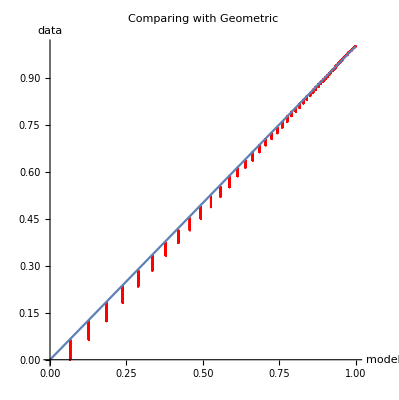

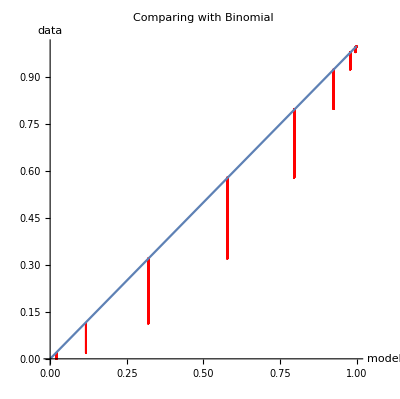

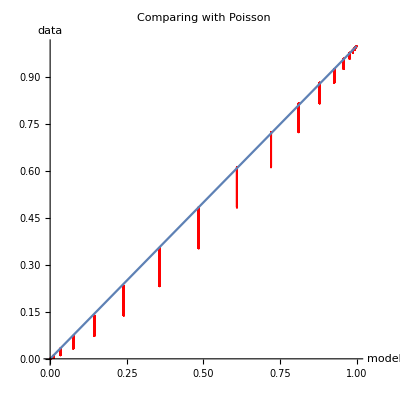

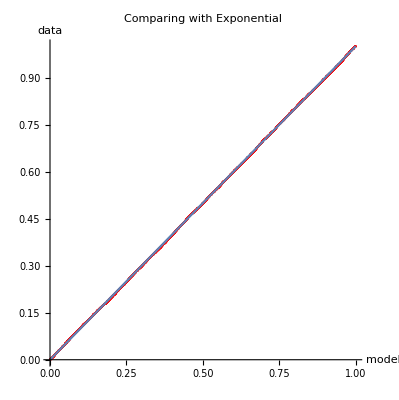

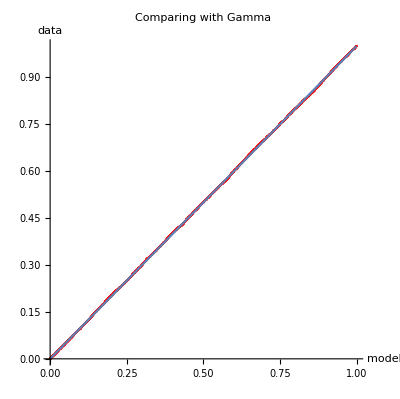

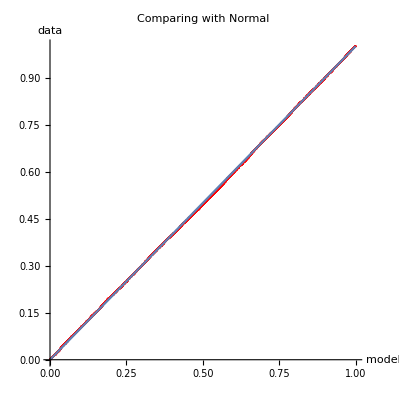

```mathematica
Show[dataplotGeoDist𝕩2, lineplot] 
Show[dataplotBinDist𝕩5, lineplot] 
Show[dataplotPoDist𝕩6, lineplot] 
Show[dataplotExpDist𝕩1, lineplot] 
Show[dataplotGammaDist𝕩3,lineplot]
Show[dataplotNormalDist𝕩4,lineplot]
```

Point Estimate

#### Setup

```mathematica
(* Import library *)
Needs["HypothesisTesting`"]
```

#### Distribution 𝕩1

```mathematica
Clear[λ];
FindDistributionParameters[𝕩1,ExponentialDistribution[λ]]
expectedValue=Mean[𝕩1];
λ=1/expectedValue (* Only for Exp.. Specific cases *)
```

{λ→4.44314}

4.44314

#### Distribution 𝕩2

```mathematica
Clear[p];
FindDistributionParameters[𝕩2,GeometricDistribution[p]]
```

{p→0.065767}

#### Distribution 𝕩3

```mathematica
Clear[α,β];
FindDistributionParameters[𝕩3,GammaDistribution[α,β]]
```

{α→7.95236,β→1.60945}

#### Distribution 𝕩4

```mathematica
Clear[μ,σ];
FindDistributionParameters[𝕩4,NormalDistribution[μ,σ]]
```

{μ→2.99474,σ→4.98621}

#### Distribution 𝕩5

```mathematica
Clear[n,p];
FindDistributionParameters[𝕩5,NormalDistribution[n,p]]
```

{n→3.2671,p→1.49972}

#### Distribution 𝕩6

```mathematica
Clear[μ];
FindDistributionParameters[𝕩6,PoissonDistribution[μ]]
```

{μ→9.7859}

Confidence Interval

```mathematica
(* According to the central limit theorem, the estimate X^—=1/n∑_(i=1)^n Subscript[X, i] will approach Normal Distribution, if the sample size is large enough. The needed size is dependent on the distribution Subscript[X, i]. if Subscript[X, i] has symmetric distribution and iid(independant identical distributed) it's often enough with a sample size of 20. *)
```

#### Setup

None

```mathematica
(* The interval should not be longer than 10 % of its mean() 
Central Limit Theorem states that the estimate will approach normal distribution if the sample size is large enough.
Notice that when Subscript[X, i]∉𝒩(μ,σ) the given confidence intervals are approximate and that you have to ensure large enough sample size. *)
```

#### Distribution 𝕩1

```mathematica
(* For large λ (over 5k...) *)
Clear[λ,ciλlen, 𝒟, TenProcentOfMean];
m=100;
𝒟=EstimatedDistribution[𝕩1,ExponentialDistribution[λ]];
List@@𝒟;
(* repeat enough times so that the CLT gives us good confidence intervals *)
𝕩1List={};
For[i=0,i<50,i++,AppendTo[𝕩1List, {randomNumber[1,100]}]];
𝕩1List=Flatten[𝕩1List,1];
findλ[data_]:=List@@EstimatedDistribution[data,ExponentialDistribution[λ]];
𝕒=findλ/@𝕩1List;
TenProcentOfMean=Mean[𝕩1]/10  //N
(* a was false at 50 so we raised to 60 *)
ciλ=MeanCI[𝕒, ConfidenceLevel->0.95]
ciλlen=(ciλ[[2]]-ciλ[[1]])
Boolean[ciλlen[[1]]<TenProcentOfMean]
```

0.0225066

{{4.35818},{4.6186}}

{0.260422}

Boolean[False]

#### Distribution 𝕩2

```mathematica
(* For large λ (over 5k...) *)
Clear[p,ciplen, 𝒟, TenProcentOfMean];
m=100;
𝒟=EstimatedDistribution[𝕩2,GeometricDistribution[p]];
List@@𝒟;
(* repeat enough times so that the CLT gives us good confidence intervals *)
𝕩2List={};
For[i=0,i<50,i++,AppendTo[𝕩2List, {randomNumber[2,100]}]];
𝕩2List=Flatten[𝕩2List,1];
findλ[data_]:=List@@EstimatedDistribution[data,GeometricDistribution[p]];
𝕒=findλ/@𝕩2List;
TenProcentOfMean=Mean[𝕩2]/10  //N
(* a was false at 50 so we raised to 60 *)
cip=MeanCI[𝕒, ConfidenceLevel->0.95]
ciplen=(cip[[2]]-cip[[1]])
Boolean[ciplen[[1]]<TenProcentOfMean]
```

1.42052

{{0.0644903},{0.0684195}}

{0.00392925}

Boolean[True]

#### Distribution 𝕩3

```mathematica
(* Comment Gamma? Example..*)
```

```mathematica
(* confidence interval for μ *)
MeanCI[𝕩3, ConfidenceLevel->0.95];
(* confidence interval for σ^2 *)
VarianceCI[𝕩3,ConfidenceLevel->0.95];
(* confidence interval for σ *)
√VarianceCI[𝕩3,ConfidenceLevel->0.95];
```

General::munfl: 0.00038413^4999.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-37579.8] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-37579.8] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
Clear[α,β];
m=100;
𝒟=EstimatedDistribution[𝕩3,GammaDistribution[α,β]];
List@@𝒟;
```

```mathematica
(* repeat enough times so that the CLT gives us good confidence intervals *)
𝕩3List={};
randomNumber[3,100];
For[i=0,i<50,i++,AppendTo[𝕩3List, {randomNumber[3,100]}]]
𝕩3List=Flatten[𝕩3List,1];
findαβ[data_]:=List@@EstimatedDistribution[data,GammaDistribution[α,β]]
{𝕒,𝕓}=Transpose[findαβ/@𝕩3List];
TenProcentOfMean=Mean[𝕩3]/10;
```

```mathematica
ciα=MeanCI[𝕒, ConfidenceLevel->0.95]
ciαlen=(ciα[[2]]-ciα[[1]]);
Boolean[ciαlen<TenProcentOfMean]
```

{7.92989,8.51787}

Boolean[True]

```mathematica
ciβ=MeanCI[𝕓, ConfidenceLevel->0.95]
ciβlen=(ciβ[[2]]-ciβ[[1]]);
Boolean[ciβlen<TenProcentOfMean]
```

{1.52824,1.64327}

Boolean[True]

#### Distribution 𝕩4

```mathematica
(* Easy case.. X ∈ N(μ,σ)*)
```

```mathematica
Clear[μ,σ,𝒟, TenProcentOfMean];
m=100;
𝒟=EstimatedDistribution[𝕩4,NormalDistribution[μ,σ]];
List@@𝒟;
(* repeat enough times so that the CLT gives us good confidence intervals *)
𝕩4List={};
For[i=0,i<50,i++,AppendTo[𝕩4List, {randomNumber[4,100]}]];
𝕩4List=Flatten[𝕩4List,1];
findμσ[data_]:=List@@EstimatedDistribution[data,NormalDistribution[μ,σ]];
{𝕒,𝕓}=Transpose[findμσ/@𝕩4List];
TenProcentOfMean=Mean[𝕩4]/10;
(* a was false at 50 so we raised to 60 *)
ciμ=MeanCI[𝕒, ConfidenceLevel->0.95]
ciμlen=(ciμ[[2]]-ciμ[[1]]);
Boolean[ciμlen<TenProcentOfMean]

ciσ=MeanCI[𝕓, ConfidenceLevel->0.95]
ciσlen=(ciσ[[2]]-ciσ[[1]]);
Boolean[ciσlen<TenProcentOfMean]
```

{2.81044,3.09833}

Boolean[True]

{4.92141,5.08976}

Boolean[True]

#### Distribution 𝕩5

```mathematica
(* For large n approximation X ∈ N(np, √(np(1-p))) *)
```

```mathematica
Clear[n,p,𝒟, TenProcentOfMean];
m=100;
𝒟=EstimatedDistribution[𝕩5,BinomialDistribution[n, p]];
List@@𝒟;
(* repeat enough times so that the CLT gives us good confidence intervals *)
𝕩5List={};
For[i=0,i<50,i++,AppendTo[𝕩5List, {randomNumber[5,100]}]];
𝕩5List=Flatten[𝕩5List,1];
findnp[data_]:=List@@EstimatedDistribution[data,BinomialDistribution[n, p]];
{𝕒,𝕓}=Transpose[findnp/@𝕩5List];
TenProcentOfMean=Mean[𝕩5]/10  //N
(* a was false at 50 so we raised to 60 *)
cin=MeanCI[𝕒, ConfidenceLevel->0.95]
cinlen=(cin[[2]]-cin[[1]])
Boolean[cinlen<TenProcentOfMean]

cip=MeanCI[𝕓, ConfidenceLevel->0.95]
ciplen=(cip[[2]]-cip[[1]])
Boolean[ciplen<TenProcentOfMean]
```

0.32671

{11.0317,14.9283}

3.89669

Boolean[False]

{0.269421,0.32545}

0.056029

Boolean[True]

#### Distribution 𝕩6

```mathematica
(* For large μ, X∈ N (μ, √μ) *)
```

```mathematica
Clear[μ,ciμlen, 𝒟, TenProcentOfMean];
m=100;
𝒟=EstimatedDistribution[𝕩6,PoissonDistribution[μ]];
List@@𝒟;
(* repeat enough times so that the CLT gives us good confidence intervals *)
𝕩6List={};
For[i=0,i<50,i++,AppendTo[𝕩6List, {randomNumber[6,100]}]];
𝕩6List=Flatten[𝕩6List,1];
findμ[data_]:=List@@EstimatedDistribution[data,PoissonDistribution[μ]];
𝕒=findμ/@𝕩6List;
TenProcentOfMean=Mean[𝕩6]/10  //N
(* a was false at 50 so we raised to 60 *)
ciμ=MeanCI[𝕒, ConfidenceLevel->0.95]
ciμlen=(ciμ[[2]]-ciμ[[1]])
Boolean[ciμlen[[1]]<TenProcentOfMean]
```

0.97859

{{9.79832},{9.97968}}

{0.181361}

Boolean[True]